```mathematica
mati22={{1,1,0,0,0,0},{0,0,0,0,Exp[ⅈ*k1*Sqrt[1-r2/k1]*L],Exp[-ⅈ*k1*Sqrt[1-r2/k1]*L]},{Exp[ⅈ*k1*(L-L2-2d)],Exp[-ⅈ*k1*(L-L2-2d)],-Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],-Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],0,0},{0,0,Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],-Exp[ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)],-Exp[-ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)]},{k1*Exp[ⅈ*k1*(L-L2-2d)],-k1*Exp[-ⅈ*k1*(L-L2-2d)],-k1*Sqrt[1-r1/k1]*Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],k1*Sqrt[1-r1/k1]*Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],0,0},{0,0,k1*Sqrt[1-r1/k1]*Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],-k1*Sqrt[1-r1/k1]*Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],-k1*Sqrt[1-r2/k1]*Exp[ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)],k1*Sqrt[1-r2/k1]*Exp[-ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)]}}
```

{{1,1,0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 L √(1-r2/k1)),ⅇ^(-ⅈ k1 L √(1-r2/k1))},{ⅇ^(ⅈ k1 (-2 d+L-L2)),ⅇ^(-ⅈ k1 (-2 d+L-L2)),-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1/k1)),-ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1/k1)),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1/k1)),ⅇ^(-ⅈ k1 (L-L2) √(1-r1/k1)),-ⅇ^(ⅈ k1 (L-L2) √(1-r2/k1)),-ⅇ^(-ⅈ k1 (L-L2) √(1-r2/k1))},{ⅇ^(ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(-ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1/k1)) k1 √(1-r1/k1),ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1/k1)) k1 √(1-r1/k1),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(-ⅈ k1 (L-L2) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(ⅈ k1 (L-L2) √(1-r2/k1)) k1 √(1-r2/k1),ⅇ^(-ⅈ k1 (L-L2) √(1-r2/k1)) k1 √(1-r2/k1)}}

```mathematica
Det[mati22]
```

ⅇ^(-2 ⅈ k1 (-2 d+L-L2)-2 ⅈ k1 (L-L2) √((k1-r1)/k1)-2 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)-ⅈ k1 L √((k1-r2)/k1)-2 ⅈ k1 (L-L2) √((k1-r2)/k1)) k1^2 (-ⅇ^(ⅈ k1 L √((k1-r2)/k1)+ⅈ k1 L √(1-r2/k1)) (-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)) (-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))+ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)) √(1-r1/k1)-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)-ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)) √(1-r1/k1))+ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)-ⅈ k1 (L-L2) √(1-r2/k1)) (ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))+ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1))-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)-ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1))) √(1-r2/k1))+ⅇ^(ⅈ k1 L √((k1-r2)/k1)-ⅈ k1 L √(1-r2/k1)) (-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+2 ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))+ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)) √(1-r1/k1)-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)-ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)) √(1-r1/k1))-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)+ⅈ k1 (L-L2) √(1-r2/k1)) (ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))+ⅇ^(ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1))-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)-ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1))) √(1-r2/k1)))

```mathematica
Simplify[%]
```

ⅇ^(ⅈ k1 (L2+2 L2 √(1-r1/k1)+2 d (1+√(1-r1/k1))+L2 √(1-r2/k1)+L (-1-2 √(1-r1/k1)-2 √(1-r2/k1)))) k1 (ⅇ^(2 ⅈ k1 ((L-L2) √(1-r1/k1)+L √(1-r2/k1))) (r1-k1 (-1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1/k1)+(L-L2) √(1-r2/k1))) (-r1+k1 (-1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 ((-2 d+L-L2) √(1-r1/k1)+L √(1-r2/k1))) (-r1-k1 (1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (1+√(1-r1/k1)+√(1-r2/k1)))) (r1+k1 (1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (L-L2) (√(1-r1/k1)+√(1-r2/k1))) (-r1-k1 (-1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1/k1)+L √(1-r2/k1))) (r1+k1 (-1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 ((-2 d+L-L2) √(1-r1/k1)+(L-L2) √(1-r2/k1))) (r1-k1 (1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(L-L2) √(1-r1/k1)+L √(1-r2/k1))) (-r1+k1 (1+√(1-r1/k1)) (1+√(1-r2/k1))))

```mathematica
matifin1[k1_,L_,L2_,d_,r1_,r2_]:={{1,1,0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 L √(1-r2/k1)),ⅇ^(-ⅈ k1 L √(1-r2/k1))},{ⅇ^(ⅈ k1 (-2 d+L-L2)),ⅇ^(-ⅈ k1 (-2 d+L-L2)),-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1/k1)),-ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1/k1)),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1/k1)),ⅇ^(-ⅈ k1 (L-L2) √(1-r1/k1)),-ⅇ^(ⅈ k1 (L-L2) √(1-r2/k1)),-ⅇ^(-ⅈ k1 (L-L2) √(1-r2/k1))},{ⅇ^(ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(-ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1/k1)) k1 √(1-r1/k1),ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1/k1)) k1 √(1-r1/k1),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(-ⅈ k1 (L-L2) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(ⅈ k1 (L-L2) √(1-r2/k1)) k1 √(1-r2/k1),ⅇ^(-ⅈ k1 (L-L2) √(1-r2/k1)) k1 √(1-r2/k1)}}
```

```mathematica
detmatifin1[k1_,L_,L2_,d_,r1_,r2_]:=ⅇ^(ⅈ k1 (L2+2 L2 √(1-r1/k1)+2 d (1+√(1-r1/k1))+L2 √(1-r2/k1)+L (-1-2 √(1-r1/k1)-2 √(1-r2/k1)))) k1 (ⅇ^(2 ⅈ k1 ((L-L2) √(1-r1/k1)+L √(1-r2/k1))) (r1-k1 (-1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1/k1)+(L-L2) √(1-r2/k1))) (-r1+k1 (-1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 ((-2 d+L-L2) √(1-r1/k1)+L √(1-r2/k1))) (-r1-k1 (1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (1+√(1-r1/k1)+√(1-r2/k1)))) (r1+k1 (1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (L-L2) (√(1-r1/k1)+√(1-r2/k1))) (-r1-k1 (-1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1/k1)+L √(1-r2/k1))) (r1+k1 (-1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 ((-2 d+L-L2) √(1-r1/k1)+(L-L2) √(1-r2/k1))) (r1-k1 (1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(L-L2) √(1-r1/k1)+L √(1-r2/k1))) (-r1+k1 (1+√(1-r1/k1)) (1+√(1-r2/k1))))
```

```mathematica
matifin2[k1_,L_,L2_,d_,r1_]:={{1,1,0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 L),ⅇ^(-ⅈ k1 L)},{ⅇ^(ⅈ k1 (-2 d+L-L2)),ⅇ^(-ⅈ k1 (-2 d+L-L2)),-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1/k1)),-ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1/k1)),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1/k1)),ⅇ^(-ⅈ k1 (L-L2) √(1-r1/k1)),-ⅇ^(ⅈ k1 (L-L2)),-ⅇ^(-ⅈ k1 (L-L2))},{ⅇ^(ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(-ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1/k1)) k1 √(1-r1/k1),ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1/k1)) k1 √(1-r1/k1),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(-ⅈ k1 (L-L2) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(ⅈ k1 (L-L2)) k1 ,ⅇ^(-ⅈ k1 (L-L2)) k1 }}
```

```mathematica
detmatifin2[k1_,L_,L2_,d_,r1_]:=-ⅇ^(ⅈ k1 (L (-3-2 √(1-r1/k1))+2 d (1+√(1-r1/k1))+2 L2 (1+√(1-r1/k1)))) k1 (-ⅇ^(2 ⅈ k1 (L+(L-L2) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (L+(-2 d+L-L2) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+2 L-2 L2+(-2 d+L-L2) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (2+√(1-r1/k1)))) r1+ⅇ^(2 ⅈ k1 (L-L2) (1+√(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))-ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(-2 d+L-L2) √(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(L-L2) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (L-L2+(-2 d+L-L2) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))
```

```mathematica
Rootie=FindRoot[Abs[detmatifin2[k1,3,1,0.5,10.8]]==0,{k1,4}]
```

{k1→2.61835}

```mathematica
Coefs=Flatten[NullSpace[matifin2[k1,3,1,0.5,10.8]/.Rootie[[1]]]]
```

{-2.95133×10^-7+0.00986967 ⅈ,2.94899×10^-7-0.00986967 ⅈ,-0.999805-0.0000298854 ⅈ,-9.32396×10^-7-2.78705×10^-11 ⅈ,-0.00986966+0.0000103109 ⅈ,-0.00986966-0.0000109009 ⅈ}

```mathematica
k11=k1/.Rootie[[1]]
```

2.61835

```mathematica
ψ[x_,r1_,r2_]:= Piecewise[{{Coefs[[1]]*Exp[ⅈ*k11*x]+Coefs[[2]]*Exp[-ⅈ*k11*x],0<=x<1.0},{Coefs[[3]]*Exp[ⅈ*k11*Sqrt[1-r1/k11]*x]+Coefs[[4]]*Exp[-ⅈ*k11*Sqrt[1-r1/k11]*x],1.0<=x<2.0},{Coefs[[5]]*Exp[ⅈ*k11*Sqrt[1-r2/k11]*x]+Coefs[[6]]*Exp[-ⅈ*k11*Sqrt[1-r2/k11]*x],2.0<=x<3}}]
```

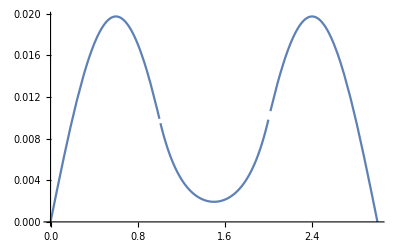

```mathematica
Plot[Abs[ψ[x,10.8,0.0]],{x,0,3},PlotRange->Full]
```

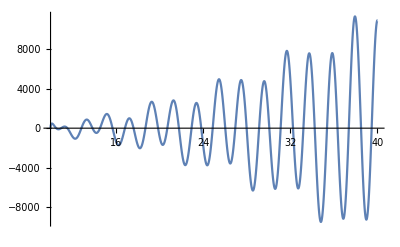

```mathematica
Plot[Im[detmatifin2[k1,3,1,0.5,10]],{k1,10,40},PlotRange->All,PlotPoints->2000]
```

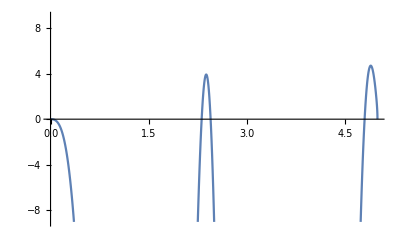

```mathematica
Plot[Re[detmatifin2[k1,3,1,0.5,5]],{k1,0,5},PlotRange->{{0,5},{-9,9}},PlotPoints->600]
```

```mathematica
Manipulate[Plot[Re[detmatifin2[k1,3,1,0.5,V]],{k1,0,V},PlotRange->{{0,V},{-5,5}},PlotPoints->600],{V,2,10}]
```

```mathematica
Manipulate[Plot[Re[detmatifin2[k1,2+J,J,0.5,6]],{k1,0,6},PlotRange->{{0,7},{-400,400}},PlotPoints->600],{J,1,2.5}]
```

```mathematica
Manipulate[Plot[Im[detmatifin2[k1,2+J,J,0.5,6]],{k1,6,12},PlotRange->{{6,13},{-400,400}},PlotPoints->600],{J,1,2.5}]
```

```mathematica
-ⅇ^(ⅈ k1 (L (-3-2 √(1-r1/k1))+2 d (1+√(1-r1/k1))+2 L2 (1+√(1-r1/k1)))) k1 (-ⅇ^(2 ⅈ k1 (L+(L-L2) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (L+(-2 d+L-L2) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+2 L-2 L2+(-2 d+L-L2) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (2+√(1-r1/k1)))) r1+ⅇ^(2 ⅈ k1 (L-L2) (1+√(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))-ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(-2 d+L-L2) √(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(L-L2) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (L-L2+(-2 d+L-L2) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))/.L->1+2d+L2
```

-ⅇ^(ⅈ k1 ((1+2 d+L2) (-3-2 √(1-r1/k1))+2 d (1+√(1-r1/k1))+2 L2 (1+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+√(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d-2 L2+2 (1+2 d+L2)+√(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (-2 d+(1+2 d) (2+√(1-r1/k1)))) r1+ⅇ^(2 ⅈ (1+2 d) k1 (1+√(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d+L2)+√(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d+L2)+(1+2 d) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d+√(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))

```mathematica
Simplify[%]
```

ⅇ^(-ⅈ k1 (1+L2+2 d √(1-r1/k1))) k1 (-(-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1))) r1+2 k1 (-1-√(1-r1/k1)+ⅇ^(4 ⅈ d k1 √(1-r1/k1)) (1-√(1-r1/k1))+ⅇ^(2 ⅈ k1 (1+L2)) (-1+√(1-r1/k1))+ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))) (1+√(1-r1/k1))))

```mathematica
Detmat[k1_,L2_,d_,r1_]:=ⅇ^(-ⅈ k1 (1+L2+2 d √(1-r1/k1))) k1 (-(-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1))) r1+2 k1 (-1-√(1-r1/k1)+ⅇ^(4 ⅈ d k1 √(1-r1/k1)) (1-√(1-r1/k1))+ⅇ^(2 ⅈ k1 (1+L2)) (-1+√(1-r1/k1))+ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))) (1+√(1-r1/k1))))
```

```mathematica
Detmat2[k1_,L2_,d_,r1_]:=ⅇ^(-ⅈ k1 (1+L2+2 d √(1-r1/k1))) k1 (-(-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1))) r1+2 k1 (ⅇ^(4 ⅈ d k1 √(1-r1/k1))(1-√(1-r1/k1))(1 -ⅇ^(2 ⅈ k1 (1+L2-2 d √(1-r1/k1))) )+(ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))) -1)(1+√(1-r1/k1))))
```

```mathematica
Detmat3[k1_,L2_,d_,r1_]:=ⅇ^(-ⅈ k1 (1+L2+2 d √(1-r1/k1))) k1 (-(-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1))) r1+2 k1 (ⅇ^(4 ⅈ d k1 √(1-r1/k1))(1 -ⅇ^(2 ⅈ k1 (1+L2-2 d √(1-r1/k1))) )(r1/k1)+(ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))) -1)(1+√(1-r1/k1))^2)/(1+√(1-r1/k1)))
```

```mathematica
Detmat4[k1_,L2_,d_,r1_]:= (2 ⅇ^(-ⅈ k1 (1+L2+2 d √(1-r1/k1))) k1^2)/(1+√(1-r1/k1))((ⅇ^(4 ⅈ d k1 √(1-r1/k1))(1 -ⅇ^(2 ⅈ k1 (1+L2-2 d √(1-r1/k1))) )(r1/k1)-(-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2))r1/(2k1)(1+√(1-r1/k1)) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1))) +(ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))) -1)(1+√(1-r1/k1))^2))
```

```mathematica
Detmat5[k1_,L2_,d_,r1_]:= (2 k1^2)/(1+√(1-r1/k1))((ⅇ^(-ⅈ k1 (1+L2-2 d √(1-r1/k1)))(1 -ⅇ^(2 ⅈ k1 (1+L2-2 d √(1-r1/k1))) )(r1/k1)-ⅇ^(-ⅈ k1 (1+L2))(-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2))r1/(2k1)(1+√(1-r1/k1)) (ⅇ^(ⅈ k1 2 d √(1-r1/k1))-ⅇ^(-ⅈ k1 2 d √(1-r1/k1))) +(ⅇ^(ⅈ k1 (1+L2+2 d √(1-r1/k1))) -ⅇ^(-ⅈ k1 (1+L2+2 d √(1-r1/k1))))(1+√(1-r1/k1))^2))
```

```mathematica
Detmat5[k1_,L2_,d_,r1_]:= (4 ⅈ k1^2)/(1+√(1-r1/k1))(-ⅇ^(-ⅈ k1 (1+L2))(-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2))r1/(2k1)(1+√(1-r1/k1)) Sin[ k1 2 d √(1-r1/k1)] +Sin[ k1 (1+L2+2 d √(1-r1/k1))](1+√(1-r1/k1))^2-Sin[  k1 (1+L2-2 d √(1-r1/k1))](r1/k1))
```

```mathematica
ⅇ^(-ⅈ k1 (1+L2))(-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2))
```

ⅇ^(-ⅈ k1 (1+L2)) (-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2))

```mathematica
FullSimplify[ⅇ^(-ⅈ k1 (1+L2)) (-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2))]
```

-4 Sin[k1] Sin[k1 L2]

```mathematica
Detmat6[k1_,L2_,d_,r1_]:= (4 ⅈ k1^2)/(1+√(1-r1/k1))(2 Sin[k1] Sin[k1 L2] r1/k1(1+√(1-r1/k1)) Sin[ k1 2 d √(1-r1/k1)] +Sin[ k1 (1+L2+2 d √(1-r1/k1))](1+√(1-r1/k1))^2-Sin[  k1 (1+L2-2 d √(1-r1/k1))](r1/k1))
```

```mathematica
-ⅇ^(ⅈ k1 ((1+2 d+L2) (-3-2 ⅈ √(r1/k1-1))+2 d (1+ⅈ √(r1/k1-1))+2 L2 (1+ⅈ √(r1/k1-1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ √(r1/k1-1))) r1+ⅇ^(2 ⅈ k1 (-2 d-2 L2+2 (1+2 d+L2)+ⅈ √(r1/k1-1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d)ⅈ √(r1/k1-1))) r1-ⅇ^(2 ⅈ k1 (-2 d+(1+2 d) (2+ⅈ √(r1/k1-1)))) r1+ⅇ^(2 ⅈ (1+2 d) k1 (1+ⅈ √(r1/k1-1))) (r1+2 k1 (-1+ⅈ √(r1/k1-1)))-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d+L2)+ⅈ √(r1/k1-1))) (r1+2 k1 (-1+ⅈ √(r1/k1-1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d+L2)+(1+2 d)ⅈ √(r1/k1-1))) (r1-2 k1 (1+ⅈ √(r1/k1-1)))+ⅇ^(2 ⅈ k1 (1+2 d+ⅈ √(r1/k1-1))) (-r1+2 k1 (1+ⅈ √(r1/k1-1))))
```

-ⅇ^(ⅈ k1 (2 d (1+ⅈ √(-1+r1/k1))+2 L2 (1+ⅈ √(-1+r1/k1))+(1+2 d+L2) (-3-2 ⅈ √(-1+r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ √(-1+r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d-2 L2+2 (1+2 d+L2)+ⅈ √(-1+r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ (1+2 d) √(-1+r1/k1))) r1-ⅇ^(2 ⅈ k1 (-2 d+(1+2 d) (2+ⅈ √(-1+r1/k1)))) r1+ⅇ^(2 ⅈ (1+2 d) k1 (1+ⅈ √(-1+r1/k1))) (r1+2 k1 (-1+ⅈ √(-1+r1/k1)))-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d+L2)+ⅈ √(-1+r1/k1))) (r1+2 k1 (-1+ⅈ √(-1+r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d+L2)+ⅈ (1+2 d) √(-1+r1/k1))) (r1-2 k1 (1+ⅈ √(-1+r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d+ⅈ √(-1+r1/k1))) (-r1+2 k1 (1+ⅈ √(-1+r1/k1))))

```mathematica
Simplify[%]
```

ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) k1 ((-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 d k1 √(-1+r1/k1))) r1+k1 (2-2 ⅈ √(-1+r1/k1)+ⅇ^(4 d k1 √(-1+r1/k1)) (-2-2 ⅈ √(-1+r1/k1))+ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(-1+r1/k1))) (-2+2 ⅈ √(-1+r1/k1))+ⅇ^(2 ⅈ k1 (1+L2)) (2+2 ⅈ √(-1+r1/k1))))

```mathematica
Detmat21[k1_,L2_,d_,r1_]:=ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(r1/k1-1))) k1 ((-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 d k1 √(r1/k1-1))) r1+2k1 (1- ⅈ √(r1/k1-1)+ⅇ^(4 d k1 √(-1+r1/k1)) (-1- ⅈ √(r1/k1-1))+ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(r1/k1-1))) (-1+ ⅈ √(r1/k1-1))+ⅇ^(2 ⅈ k1 (1+L2)) (1+ ⅈ √(r1/k1-1))))
```

```mathematica
Detmat22[k1_,L2_,d_,r1_]:=ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(r1/k1-1))) k1 ((-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 d k1 √(r1/k1-1))) r1+2k1 (ⅇ^(4 d k1 √(-1+r1/k1)) (-1- ⅈ √(r1/k1-1))+(1-ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(r1/k1-1))) )(1- ⅈ √(r1/k1-1))+ⅇ^(2 ⅈ k1 (1+L2)) (1+ ⅈ √(r1/k1-1))))
```

```mathematica
Detmat21[k1,L2,d,r1]-Detmat22[k1,L2,d,r1]
```

-ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) k1 ((-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 d k1 √(-1+r1/k1))) r1+2 k1 (ⅇ^(4 d k1 √(-1+r1/k1)) (-1-ⅈ √(-1+r1/k1))+(1-ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(-1+r1/k1)))) (1-ⅈ √(-1+r1/k1))+ⅇ^(2 ⅈ k1 (1+L2)) (1+ⅈ √(-1+r1/k1))))+ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) k1 ((-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 d k1 √(-1+r1/k1))) r1+2 k1 (1-ⅈ √(-1+r1/k1)+ⅇ^(4 d k1 √(-1+r1/k1)) (-1-ⅈ √(-1+r1/k1))+ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(-1+r1/k1))) (-1+ⅈ √(-1+r1/k1))+ⅇ^(2 ⅈ k1 (1+L2)) (1+ⅈ √(-1+r1/k1))))

```mathematica
Simplify[%]
```

0

```mathematica
Detmat23[k1_,L2_,d_,r1_]:=ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(r1/k1-1))) k1 ((-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 d k1 √(r1/k1-1))) r1+2k1 ((1-ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(r1/k1-1))) )(1- ⅈ √(r1/k1-1))+(ⅇ^(2 ⅈ k1 (1+L2)) -ⅇ^(4 d k1 √(r1/k1-1)) )(1+ ⅈ √(r1/k1-1))))
```

```mathematica
Detmat24[k1_,L2_,d_,r1_]:=ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(r1/k1-1))) k1 ((-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2)) (-1+ⅇ^(4 d k1 √(r1/k1-1))) r1+2k1 ((1-ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(r1/k1-1))) )(1- ⅈ √(r1/k1-1))+(ⅇ^(2 ⅈ k1 (1+L2)) -ⅇ^(4 d k1 √(r1/k1-1)) )(1+ ⅈ √(r1/k1-1))))
```

```mathematica
ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(r1/k1-1)))(-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2))
```

ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) (-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2))

```mathematica
FullSimplify[ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(r1/k1-1))) (-1+ⅇ^(2 ⅈ k1)) (-1+ⅇ^(2 ⅈ k1 L2))]
```

-4 ⅇ^(-2 d k1 √(-1+r1/k1)) Sin[k1] Sin[k1 L2]

```mathematica
ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(r1/k1-1)))(1-ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(r1/k1-1))) )
```

ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) (1-ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(-1+r1/k1))))

```mathematica
Simplify[ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) (1-ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(-1+r1/k1))))]
```

ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) (1-ⅇ^(k1 (2 ⅈ+2 ⅈ L2+4 d √(-1+r1/k1))))

```mathematica
(ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1)))-ⅇ^(k1 ( ⅈ+ ⅈ L2+2 d √(-1+r1/k1))))
```

ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1)))-ⅇ^(k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1)))

```mathematica
Simplify[ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1)))-ⅇ^(k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1)))]
```

ⅇ^(-ⅈ k1 (1+L2-2 ⅈ d √(-1+r1/k1)))-ⅇ^(k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1)))

```mathematica
ExpToTrig[ⅇ^(-ⅈ k1 (1+L2-2 ⅈ d √(-1+r1/k1)))-ⅇ^(k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1)))]
```

-2 ⅈ Sin[k1+k1 L2-2 ⅈ d k1 √(-1+r1/k1)]

```mathematica
Simplify[-2 ⅈ Sin[k1+k1 L2-2 ⅈ d k1 √(-1+r1/k1)]]
```

-2 ⅈ Sin[k1 (1+L2-2 ⅈ d √(-1+r1/k1))]

```mathematica
-2 ⅈ( Sin[k1 (1+L2)]Cos[k1 (2 ⅈ d √(-1+r1/k1))]- Sin[k1 (2 ⅈ d √(-1+r1/k1))]Cos[k1 (1+L2)])
```

-2 ⅈ (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]-ⅈ Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2)) -ⅇ^(4 d k1 √(r1/k1-1)) )
```

ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 d k1 √(-1+r1/k1)))

```mathematica
Simplify[ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 d k1 √(-1+r1/k1)))]
```

ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 d k1 √(-1+r1/k1)))

```mathematica
ExpToTrig[ⅇ^(-k1 (ⅈ+ⅈ L2+2 d √(-1+r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 d k1 √(-1+r1/k1)))]
```

(Cos[k1+k1 L2-2 ⅈ d k1 √(-1+r1/k1)]-ⅈ Sin[k1+k1 L2-2 ⅈ d k1 √(-1+r1/k1)]) (Cos[2 k1 (1+L2)]-Cosh[4 d k1 √(-1+r1/k1)]+ⅈ Sin[2 k1 (1+L2)]-Sinh[4 d k1 √(-1+r1/k1)])

```mathematica
Simplify[(Cos[k1+k1 L2-2 ⅈ d k1 √(-1+r1/k1)]-ⅈ Sin[k1+k1 L2-2 ⅈ d k1 √(-1+r1/k1)]) (Cos[2 k1 (1+L2)]-Cosh[4 d k1 √(-1+r1/k1)]+ⅈ Sin[2 k1 (1+L2)]-Sinh[4 d k1 √(-1+r1/k1)])]
```

2 ⅈ Sin[k1 (1+L2+2 ⅈ d √(-1+r1/k1))]

```mathematica
2 ⅈ (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+ⅈ Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)])
```

2 ⅈ (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+ⅈ Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
Detmat25[k1_,L2_,d_,r1_]:= k1 (-4 ⅇ^(-2 d k1 √(-1+r1/k1)) Sin[k1] Sin[k1 L2](-1+ⅇ^(4 d k1 √(r1/k1-1))) r1+2k1 ((-2 ⅈ (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]-ⅈ Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]))(1- ⅈ √(r1/k1-1))+(2 ⅈ (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+ⅈ Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]) )(1+ ⅈ √(r1/k1-1))))
```

```mathematica
k1 (-4 ⅇ^(-2 d k1 √(-1+r1/k1)) Sin[k1] Sin[k1 L2](-1+ⅇ^(4 d k1 √(r1/k1-1))) r1+2k1 ((-2 ⅈ (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]-ⅈ Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]))(1- ⅈ √(r1/k1-1))+(2 ⅈ (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+ⅈ Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]) )(1+ ⅈ √(r1/k1-1))))
```

k1 (-4 ⅇ^(-2 d k1 √(-1+r1/k1)) (-1+ⅇ^(4 d k1 √(-1+r1/k1))) r1 Sin[k1] Sin[k1 L2]+2 k1 (-2 ⅈ (1-ⅈ √(-1+r1/k1)) (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]-ⅈ Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)])+2 ⅈ (1+ⅈ √(-1+r1/k1)) (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+ⅈ Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)])))

```mathematica
Simplify[%]
```

-4 ⅇ^(-2 d k1 √(-1+r1/k1)) k1 ((-1+ⅇ^(4 d k1 √(-1+r1/k1))) k1 Cos[k1 (1+L2)]+(-1+ⅇ^(4 d k1 √(-1+r1/k1))) r1 Sin[k1] Sin[k1 L2]+(1+ⅇ^(4 d k1 √(-1+r1/k1))) k1 √(-1+r1/k1) Sin[k1 (1+L2)])

```mathematica
Detmat26[k1_,L2_,d_,r1_]:=-4 ⅇ^(-2 d k1 √(-1+r1/k1)) k1 ((-1+ⅇ^(4 d k1 √(-1+r1/k1))) k1 Cos[k1 (1+L2)]+(-1+ⅇ^(4 d k1 √(-1+r1/k1))) r1 Sin[k1] Sin[k1 L2]+(1+ⅇ^(4 d k1 √(-1+r1/k1))) k1 √(-1+r1/k1) Sin[k1 (1+L2)])
```

```mathematica
Detmat27[k1_,L2_,d_,r1_]:=-8  k1 (Sinh[2 d k1 √(r1/k1-1)] k1 Cos[k1 (1+L2)]+Sinh[2 d k1 √(r1/k1-1)]  r1 Sin[k1] Sin[k1 L2]+ k1 √(r1/k1-1)Cosh[2 d k1 √(r1/k1-1)]  Sin[k1 (1+L2)])
```

```mathematica
Detmat17[k1_,L2_,d_,r1_]:=(4  k1)/(1+√(1-r1/k1)) (2 r1 (1+√(1-r1/k1)) Sin[k1] Sin[k1 L2] Sin[2 d k1 √(1-r1/k1)]-r1 Sin[k1 (1+L2-2 d √(1-r1/k1))]+(-r1+2 k1 (1+√(1-r1/k1))) Sin[k1 (1+L2+2 d √(1-r1/k1))])
```

```mathematica
Fulldet[k1_,L2_,d_,r1_]:=Piecewise[{{Detmat27[k1,L2,d,r1],k1<r1},{Detmat17[k1,L2,d,r1],k1>r1}}]
```

```mathematica
Manipulate[Plot[Fulldet[k1,J,0.5,6],{k1,0,12},PlotRange->{{0,13},{-40,40}},PlotPoints->600],{J,1,2.5}]
```

```mathematica
Manipulate[Plot[Fulldet[k1,1,0.5,r],{k1,0,12},PlotRange->{{0,13},{-40,40}},PlotPoints->600],{r,0,10}]
```

```mathematica
-8  k1 (Sinh[2 d k1 √(r1/k1-1)] k1 Cos[k1 (1+L2)]+Sinh[2 d k1 √(r1/k1-1)]  r1 Sin[k1] Sin[k1 L2]+ k1 √(r1/k1-1)Cosh[2 d k1 √(r1/k1-1)]  Sin[k1 (1+L2)])
```

-8 k1 (k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+k1 Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]+r1 Sin[k1] Sin[k1 L2] Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
D[(-8 k1 (k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+k1 Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]+r1 Sin[k1] Sin[k1 L2] Sinh[2 d k1 √(-1+r1/k1)])), k1]
```

-8 (k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+k1 Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]+r1 Sin[k1] Sin[k1 L2] Sinh[2 d k1 √(-1+r1/k1)])-8 k1 (k1 (1+L2) √(-1+r1/k1) Cos[k1 (1+L2)] Cosh[2 d k1 √(-1+r1/k1)]+k1 (-(d r1)/(k1 √(-1+r1/k1))+2 d √(-1+r1/k1)) Cos[k1 (1+L2)] Cosh[2 d k1 √(-1+r1/k1)]+r1 (-(d r1)/(k1 √(-1+r1/k1))+2 d √(-1+r1/k1)) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1] Sin[k1 L2]-(r1 Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)])/(2 k1 √(-1+r1/k1))+√(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]+L2 r1 Cos[k1 L2] Sin[k1] Sinh[2 d k1 √(-1+r1/k1)]+r1 Cos[k1] Sin[k1 L2] Sinh[2 d k1 √(-1+r1/k1)]-k1 (1+L2) Sin[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]+k1 √(-1+r1/k1) (-(d r1)/(k1 √(-1+r1/k1))+2 d √(-1+r1/k1)) Sin[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
Simplify[%]
```

1/(√(-1+r1/k1))(4 Cosh[2 d k1 √(-1+r1/k1)] (2 k1 (k1 (1+2 d+L2)-(1+d+L2) r1) Cos[k1 (1+L2)]+2 d (2 k1-r1) r1 Sin[k1] Sin[k1 L2]+(4 k1-3 r1) Sin[k1 (1+L2)])+8 √(-1+r1/k1) (-2 k1 Cos[k1 (1+L2)]-k1 L2 r1 Cos[k1 L2] Sin[k1]-k1 r1 Cos[k1] Sin[k1 L2]-r1 Sin[k1] Sin[k1 L2]+k1^2 Sin[k1 (1+L2)]+2 d k1^2 Sin[k1 (1+L2)]+k1^2 L2 Sin[k1 (1+L2)]-d k1 r1 Sin[k1 (1+L2)]) Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
mati2222={{Exp[ⅈ*k1*L1],Exp[-ⅈ*k1*L1],0,0,0,0},{0,0,0,0,Exp[ⅈ*k1*Sqrt[1-r2/k1]*L],Exp[-ⅈ*k1*Sqrt[1-r2/k1]*L]},{Exp[ⅈ*k1*(L-L2-2d)],Exp[-ⅈ*k1*(L-L2-2d)],-Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],-Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],0,0},{0,0,Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],-Exp[ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)],-Exp[-ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)]},{k1*Exp[ⅈ*k1*(L-L2-2d)],-k1*Exp[-ⅈ*k1*(L-L2-2d)],-k1*Sqrt[1-r1/k1]*Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],k1*Sqrt[1-r1/k1]*Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],0,0},{0,0,k1*Sqrt[1-r1/k1]*Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],-k1*Sqrt[1-r1/k1]*Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],-k1*Sqrt[1-r2/k1]*Exp[ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)],k1*Sqrt[1-r2/k1]*Exp[-ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)]}}
```

{{ⅇ^(ⅈ k1 L1),ⅇ^(-ⅈ k1 L1),0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 L √(1-r2/k1)),ⅇ^(-ⅈ k1 L √(1-r2/k1))},{ⅇ^(ⅈ k1 (-2 d+L-L2)),ⅇ^(-ⅈ k1 (-2 d+L-L2)),-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1/k1)),-ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1/k1)),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1/k1)),ⅇ^(-ⅈ k1 (L-L2) √(1-r1/k1)),-ⅇ^(ⅈ k1 (L-L2) √(1-r2/k1)),-ⅇ^(-ⅈ k1 (L-L2) √(1-r2/k1))},{ⅇ^(ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(-ⅈ k1 (-2 d+L-L2)) k1,-ⅇ^(ⅈ k1 (-2 d+L-L2) √(1-r1/k1)) k1 √(1-r1/k1),ⅇ^(-ⅈ k1 (-2 d+L-L2) √(1-r1/k1)) k1 √(1-r1/k1),0,0},{0,0,ⅇ^(ⅈ k1 (L-L2) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(-ⅈ k1 (L-L2) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(ⅈ k1 (L-L2) √(1-r2/k1)) k1 √(1-r2/k1),ⅇ^(-ⅈ k1 (L-L2) √(1-r2/k1)) k1 √(1-r2/k1)}}

```mathematica
Det[mati2222]
```

ⅇ^(-ⅈ k1 L1-2 ⅈ k1 (-2 d+L-L2)-2 ⅈ k1 (L-L2) √((k1-r1)/k1)-2 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)-ⅈ k1 L √((k1-r2)/k1)-2 ⅈ k1 (L-L2) √((k1-r2)/k1)) k1^2 (-ⅇ^(ⅈ k1 L √((k1-r2)/k1)+ⅈ k1 L √(1-r2/k1)) (-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)) (-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))+ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)) √(1-r1/k1)-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)-ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)) √(1-r1/k1))+ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)-ⅈ k1 (L-L2) √(1-r2/k1)) (ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))+ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1))-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)-ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1))) √(1-r2/k1))+ⅇ^(ⅈ k1 L √((k1-r2)/k1)-ⅈ k1 L √(1-r2/k1)) (-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+2 ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))+ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)) √(1-r1/k1)-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)-ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)) √(1-r1/k1))-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)+ⅈ k1 (L-L2) √(1-r2/k1)) (ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)+ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))+ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1))-ⅇ^(ⅈ k1 (L-L2) √((k1-r1)/k1)-ⅈ k1 (L-L2) √(1-r1/k1)+ⅈ k1 (L-L2) √((k1-r2)/k1)) (-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1))-ⅇ^(2 ⅈ k1 L1+ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1)+ⅇ^(3 ⅈ k1 (-2 d+L-L2)+3 ⅈ k1 (-2 d+L-L2) √((k1-r1)/k1)) √((k1-r1)/k1))) √(1-r2/k1)))

```mathematica
Simplify[%]
```

ⅇ^(ⅈ k1 (-L1+L2+2 L2 √(1-r1/k1)+2 d (1+√(1-r1/k1))+L2 √(1-r2/k1)+L (-1-2 √(1-r1/k1)-2 √(1-r2/k1)))) k1 (ⅇ^(2 ⅈ k1 (L1+(L-L2) √(1-r1/k1)+L √(1-r2/k1))) (r1-k1 (-1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1/k1)+(L-L2) √(1-r2/k1))) (-r1+k1 (-1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (L1+(-2 d+L-L2) √(1-r1/k1)+L √(1-r2/k1))) (-r1-k1 (1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (1+√(1-r1/k1)+√(1-r2/k1)))) (r1+k1 (1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (L1+(L-L2) (√(1-r1/k1)+√(1-r2/k1)))) (-r1-k1 (-1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1/k1)+L √(1-r2/k1))) (r1+k1 (-1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (L1+(-2 d+L-L2) √(1-r1/k1)+(L-L2) √(1-r2/k1))) (r1-k1 (1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(L-L2) √(1-r1/k1)+L √(1-r2/k1))) (-r1+k1 (1+√(1-r1/k1)) (1+√(1-r2/k1))))

```mathematica
ⅇ^(ⅈ k1 (-L1+L2+2 L2 √(1-r1/k1)+2 d (1+√(1-r1/k1))+L2 √(1-r2/k1)+L (-1-2 √(1-r1/k1)-2 √(1-r2/k1)))) k1 (ⅇ^(2 ⅈ k1 (L1+(L-L2) √(1-r1/k1)+L √(1-r2/k1))) (r1-k1 (-1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1/k1)+(L-L2) √(1-r2/k1))) (-r1+k1 (-1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (L1+(-2 d+L-L2) √(1-r1/k1)+L √(1-r2/k1))) (-r1-k1 (1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (1+√(1-r1/k1)+√(1-r2/k1)))) (r1+k1 (1+√(1-r1/k1)) (-1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (L1+(L-L2) (√(1-r1/k1)+√(1-r2/k1)))) (-r1-k1 (-1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(-2 d+L-L2) √(1-r1/k1)+L √(1-r2/k1))) (r1+k1 (-1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (L1+(-2 d+L-L2) √(1-r1/k1)+(L-L2) √(1-r2/k1))) (r1-k1 (1+√(1-r1/k1)) (1+√(1-r2/k1)))+ⅇ^(2 ⅈ k1 (-2 d+L-L2+(L-L2) √(1-r1/k1)+L √(1-r2/k1))) (-r1+k1 (1+√(1-r1/k1)) (1+√(1-r2/k1))))/.r2->0
```

ⅇ^(ⅈ k1 (-L1+2 L2+2 L2 √(1-r1/k1)+L (-3-2 √(1-r1/k1))+2 d (1+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (L+L1+(L-L2) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (L+L1+(-2 d+L-L2) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (-2 d+2 L-2 L2+(-2 d+L-L2) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (2+√(1-r1/k1)))) r1+ⅇ^(2 ⅈ k1 (L1+(L-L2) (1+√(1-r1/k1)))) (-r1-2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(-2 d+L-L2) √(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (L+L1-L2+(-2 d+L-L2) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(L-L2) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))

```mathematica
Simplify[%]
```

ⅇ^(ⅈ k1 (-L1+2 L2+2 L2 √(1-r1/k1)+L (-3-2 √(1-r1/k1))+2 d (1+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (L+L1+(L-L2) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (L+L1+(-2 d+L-L2) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (-2 d+2 L-2 L2+(-2 d+L-L2) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (2+√(1-r1/k1)))) r1+ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(-2 d+L-L2) √(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))-ⅇ^(2 ⅈ k1 (L1+(L-L2) (1+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (L+L1-L2+(-2 d+L-L2) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(L-L2) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))

```mathematica
ⅇ^(ⅈ k1 (-L1+2 L2+2 L2 √(1-r1/k1)+L (-3-2 √(1-r1/k1))+2 d (1+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (L+L1+(L-L2) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (L+L1+(-2 d+L-L2) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (-2 d+2 L-2 L2+(-2 d+L-L2) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(L-L2) (2+√(1-r1/k1)))) r1+ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(-2 d+L-L2) √(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))-ⅇ^(2 ⅈ k1 (L1+(L-L2) (1+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (L+L1-L2+(-2 d+L-L2) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d+2 L-L2+(L-L2) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))/.L->1-L1+2d+L2
```

ⅇ^(ⅈ k1 (-L1+2 L2+2 L2 √(1-r1/k1)+(1+2 d-L1+L2) (-3-2 √(1-r1/k1))+2 d (1+√(1-r1/k1)))) k1 (-ⅇ^(2 ⅈ k1 (1+2 d+L2+(1-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (-2 d-2 L2+2 (1+2 d-L1+L2)+(1-L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1-L1) √(1-r1/k1))) (r1+2 k1 (-1+√(1-r1/k1)))-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d+(1-L1) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))

```mathematica
Simplify[%]
```

ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))

```mathematica
Detmat31[k1_,L2_,L1_,d_,r1_]:=ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))
```

```mathematica
Detmat32[k1_,L1_,L2_,d_,r1_]:=ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))
```

```mathematica
Detmat33[k1_,L1_,L2_,d_,r1_]:=ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1+(ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) -ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) )(r1+2 k1 (-1+√(1-r1/k1)))+(ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) -ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))))(r1-2 k1 (1+√(1-r1/k1))))
```

```mathematica
Detmat33[k1,L1,L2,d,r1]-Detmat32[k1,L1,L2,d,r1]
```

ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1+(-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1))))+ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1))))) (r1+2 k1 (-1+√(1-r1/k1)))+(-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1)))) (r1-2 k1 (1+√(1-r1/k1))))-ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))

```mathematica
Simplify[%]
```

0

```mathematica
Detmat34[k1_,L1_,L2_,d_,r1_]:=ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1+(ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) -ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) )(r1+2 k1 (-1+√(1-r1/k1)))+(ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) -ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))))(r1-2 k1 (1+√(1-r1/k1))))
```

```mathematica
(ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1)ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1))))
```

ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1)

```mathematica
Simplify[%]
```

ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1)+ⅇ^(2 ⅈ k1 (2 L1+L2))) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1))) r1

```mathematica
(ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) -ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) )ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1))))
```

ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) (-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1))))+ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))))

```mathematica
Simplify[ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) (-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1))))+ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))))]
```

ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 ⅈ k1 (L1+d √(1-r1/k1))))

```mathematica
ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1))))*(ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) -ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))))
```

ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) (-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))))

```mathematica
Simplify[ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) (-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))))]
```

ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(4 ⅈ k1 L1)-ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))))

```mathematica
Detmat35[k1_,L1_,L2_,d_,r1_]:= k1 (ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1)+ⅇ^(2 ⅈ k1 (2 L1+L2))) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1))) r1+ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 ⅈ k1 (L1+d √(1-r1/k1))))(r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(4 ⅈ k1 L1)-ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))))(r1-2 k1 (1+√(1-r1/k1))))
```

```mathematica
Detmat35[k1,L1,L2,d,r1]-Detmat32[k1,L1,L2,d,r1]
```

k1 (ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1)+ⅇ^(2 ⅈ k1 (2 L1+L2))) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1))) r1+ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 ⅈ k1 (L1+d √(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(4 ⅈ k1 L1)-ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1)))) (r1-2 k1 (1+√(1-r1/k1))))-ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))

```mathematica
ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 ⅈ k1 (L1+d √(1-r1/k1))))
```

ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 ⅈ k1 (L1+d √(1-r1/k1))))

```mathematica
Expand[ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1 (1+L2))-ⅇ^(4 ⅈ k1 (L1+d √(1-r1/k1))))]
```

ⅇ^(2 ⅈ k1 (1+L2)-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))-ⅇ^(4 ⅈ k1 (L1+d √(1-r1/k1))-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))

```mathematica
ExpToTrig[ⅇ^(2 ⅈ k1 (1+L2)-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))-ⅇ^(4 ⅈ k1 (L1+d √(1-r1/k1))-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))]
```

2 ⅈ Sin[k1-2 k1 L1+k1 L2-2 d k1 √(1-r1/k1)]

```mathematica
ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(4 ⅈ k1 L1)-ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))))
```

ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(4 ⅈ k1 L1)-ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))))

```mathematica
Expand[ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(4 ⅈ k1 L1)-ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))))]
```

ⅇ^(4 ⅈ k1 L1-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))-ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))

```mathematica
ExpToTrig[ⅇ^(4 ⅈ k1 L1-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))-ⅇ^(2 ⅈ k1 (1+L2+2 d √(1-r1/k1))-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))]
```

-2 ⅈ Sin[k1-2 k1 L1+k1 L2+2 d k1 √(1-r1/k1)]

```mathematica
Detmat36[k1_,L1_,L2_,d_,r1_]:= k1 (ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1)+ⅇ^(2 ⅈ k1 (2 L1+L2))) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1))) r1+2 ⅈ Sin[k1-2 k1 L1+k1 L2-2 d k1 √(1-r1/k1)](r1+2 k1 (-1+√(1-r1/k1)))-2 ⅈ Sin[k1-2 k1 L1+k1 L2+2 d k1 √(1-r1/k1)](r1-2 k1 (1+√(1-r1/k1))))
```

```mathematica
ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1)+ⅇ^(2 ⅈ k1 (2 L1+L2))) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1)))
```

ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1)+ⅇ^(2 ⅈ k1 (2 L1+L2))) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1)))

```mathematica
Expand[ⅇ^(-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1)+ⅇ^(2 ⅈ k1 (2 L1+L2))) (-1+ⅇ^(4 ⅈ d k1 √(1-r1/k1)))]
```

-ⅇ^(2 ⅈ k1-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))-ⅇ^(2 ⅈ k1 (2 L1+L2)-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))+ⅇ^(2 ⅈ k1+4 ⅈ d k1 √(1-r1/k1)-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))+ⅇ^(2 ⅈ k1 (2 L1+L2)+4 ⅈ d k1 √(1-r1/k1)-ⅈ k1 (1+2 L1+L2+2 d √(1-r1/k1)))

```mathematica
ExpToTrig[%]
```

-2 ⅈ Sin[k1-2 k1 L1-k1 L2-2 d k1 √(1-r1/k1)]+2 ⅈ Sin[k1-2 k1 L1-k1 L2+2 d k1 √(1-r1/k1)]

```mathematica
Detmat37[k1_,L1_,L2_,d_,r1_]:= k1 ((-2 ⅈ Sin[k1-2 k1 L1-k1 L2-2 d k1 √(1-r1/k1)]+2 ⅈ Sin[k1-2 k1 L1-k1 L2+2 d k1 √(1-r1/k1)])r1+2 ⅈ Sin[k1-2 k1 L1+k1 L2-2 d k1 √(1-r1/k1)](r1+2 k1 (-1+√(1-r1/k1)))-2 ⅈ Sin[k1-2 k1 L1+k1 L2+2 d k1 √(1-r1/k1)](r1-2 k1 (1+√(1-r1/k1))))
```

```mathematica
k1 ((-2 ⅈ Sin[k1-2 k1 L1-k1 L2-2 d k1 √(1-r1/k1)]+2 ⅈ Sin[k1-2 k1 L1-k1 L2+2 d k1 √(1-r1/k1)])r1+2 ⅈ Sin[k1-2 k1 L1+k1 L2-2 d k1 √(1-r1/k1)](r1+2 k1 (-1+√(1-r1/k1)))-2 ⅈ Sin[k1-2 k1 L1+k1 L2+2 d k1 √(1-r1/k1)](r1-2 k1 (1+√(1-r1/k1))))
```

k1 (2 ⅈ (r1+2 k1 (-1+√(1-r1/k1))) Sin[k1-2 k1 L1+k1 L2-2 d k1 √(1-r1/k1)]+r1 (-2 ⅈ Sin[k1-2 k1 L1-k1 L2-2 d k1 √(1-r1/k1)]+2 ⅈ Sin[k1-2 k1 L1-k1 L2+2 d k1 √(1-r1/k1)])-2 ⅈ (r1-2 k1 (1+√(1-r1/k1))) Sin[k1-2 k1 L1+k1 L2+2 d k1 √(1-r1/k1)])

```mathematica
Simplify[%]
```

2 ⅈ k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1 √(1-r1/k1)]+(r1+2 k1 (-1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2-2 d √(1-r1/k1))]+(-r1+2 k1 (1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2+2 d √(1-r1/k1))])

```mathematica
Detmat38[k1_,L1_,L2_,d_,r1_]:=2 ⅈ k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1 √(1-r1/k1)]+(r1+2 k1 (-1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2-2 d √(1-r1/k1))]+(-r1+2 k1 (1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2+2 d √(1-r1/k1))])
```

```mathematica
Detmat38[k1,L1,L2,d,r1]-Detmat32[k1,L1,L2,d,r1]
```

-ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) (r1+2 k1 (-1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) (r1-2 k1 (1+√(1-r1/k1)))+ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))) (-r1+2 k1 (1+√(1-r1/k1))))+2 ⅈ k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1 √(1-r1/k1)]+(r1+2 k1 (-1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2-2 d √(1-r1/k1))]+(-r1+2 k1 (1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2+2 d √(1-r1/k1))])

```mathematica
Simplify[%]
```

0

```mathematica
Detmat39[k1_,L1_,L2_,d_,r1_]:=2  k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1 √(1-r1/k1)]+(r1+2 k1 (-1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2-2 d √(1-r1/k1))]+(-r1+2 k1 (1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2+2 d √(1-r1/k1))])
```

```mathematica
Detmat39[k1,0,L2,d,r1]-Detmat17[k1,L2,d,r1]
```

-1/(1+√(1-r1/k1))4 k1 (2 r1 (1+√(1-r1/k1)) Sin[k1] Sin[k1 L2] Sin[2 d k1 √(1-r1/k1)]-r1 Sin[k1 (1+L2-2 d √(1-r1/k1))]+(-r1+2 k1 (1+√(1-r1/k1))) Sin[k1 (1+L2+2 d √(1-r1/k1))])+2 k1 (2 r1 Cos[k1 (-1+L2)] Sin[2 d k1 √(1-r1/k1)]+(r1+2 k1 (-1+√(1-r1/k1))) Sin[k1 (1+L2-2 d √(1-r1/k1))]+(-r1+2 k1 (1+√(1-r1/k1))) Sin[k1 (1+L2+2 d √(1-r1/k1))])

```mathematica
Simplify[%]
```

0

```mathematica
Detmat41[k1_,L1_,L2_,d_,r1_]:=ⅇ^(-ⅈ k1 (3+L2+2 √(1-r1/k1)-2 L1 (1+√(1-r1/k1))+2 d (2+√(1-r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) √(1-r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) √(1-r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+√(1-r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+√(1-r1/k1)))) r1+(ⅇ^(2 ⅈ k1 (2+2 d+L2+√(1-r1/k1)-L1 (2+√(1-r1/k1)))) -ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+√(1-r1/k1)))) )(r1+2 k1 (-1+√(1-r1/k1)))+(ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) √(1-r1/k1))) -ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) √(1-r1/k1))))(r1-2 k1 (1+√(1-r1/k1))))
```

```mathematica
ⅇ^(-ⅈ k1 (3+L2+2ⅈ √(r1/k1-1)-2 L1 (1+ⅈ √(r1/k1-1))+2 d (2+ⅈ √(r1/k1-1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+(1+2 d-L1) ⅈ √(r1/k1-1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-(-1+L1) ⅈ √(r1/k1-1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+ⅈ √(r1/k1-1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+ⅈ √(r1/k1-1)))) r1+(ⅇ^(2 ⅈ k1 (2+2 d+L2+ⅈ √(r1/k1-1)-L1 (2+ⅈ √(r1/k1-1)))) -ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+ⅈ √(r1/k1-1)))) )(r1+2 k1 (-1+ⅈ √(r1/k1-1)))+(ⅇ^(2 ⅈ k1 (1+2 d-(-1+L1) ⅈ √(r1/k1-1))) -ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+(1+2 d-L1) ⅈ √(r1/k1-1))))(r1-2 k1 (1+ⅈ √(r1/k1-1))))
```

ⅇ^(-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)-2 L1 (1+ⅈ √(-1+r1/k1))+2 d (2+ⅈ √(-1+r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ (1+2 d-L1) √(-1+r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-ⅈ (-1+L1) √(-1+r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+ⅈ √(-1+r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+ⅈ √(-1+r1/k1)))) r1+(-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+ⅈ √(-1+r1/k1))))+ⅇ^(2 ⅈ k1 (2+2 d+L2+ⅈ √(-1+r1/k1)-L1 (2+ⅈ √(-1+r1/k1))))) (r1+2 k1 (-1+ⅈ √(-1+r1/k1)))+(-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+ⅈ (1+2 d-L1) √(-1+r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-ⅈ (-1+L1) √(-1+r1/k1)))) (r1-2 k1 (1+ⅈ √(-1+r1/k1))))

```mathematica
Simplify[%]
```

ⅇ^(-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+L1 (-2-2 ⅈ √(-1+r1/k1))+d (4+2 ⅈ √(-1+r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ (1+2 d-L1) √(-1+r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-ⅈ (-1+L1) √(-1+r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+ⅈ √(-1+r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+ⅈ √(-1+r1/k1)))) r1+(-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+ⅈ (1+2 d-L1) √(-1+r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-ⅈ (-1+L1) √(-1+r1/k1)))) (r1+k1 (-2-2 ⅈ √(-1+r1/k1)))+(ⅇ^(2 ⅈ k1 (2+2 d-2 L1+L2+ⅈ √(-1+r1/k1)-ⅈ L1 √(-1+r1/k1)))-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+ⅈ √(-1+r1/k1))))) (r1+k1 (-2+2 ⅈ √(-1+r1/k1))))

```mathematica
Detmat42[k1_,L1_,L2_,d_,r1_]:=ⅇ^(-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+L1 (-2-2 ⅈ √(-1+r1/k1))+d (4+2 ⅈ √(-1+r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ (1+2 d-L1) √(-1+r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-ⅈ (-1+L1) √(-1+r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+ⅈ √(-1+r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+ⅈ √(-1+r1/k1)))) r1+(-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+ⅈ (1+2 d-L1) √(-1+r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-ⅈ (-1+L1) √(-1+r1/k1)))) (r1+k1 (-2-2 ⅈ √(-1+r1/k1)))+(ⅇ^(2 ⅈ k1 (2+2 d-2 L1+L2+ⅈ √(-1+r1/k1)-ⅈ L1 √(-1+r1/k1)))-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+ⅈ √(-1+r1/k1))))) (r1+k1 (-2+2 ⅈ √(-1+r1/k1))))
```

```mathematica
Detmat42[k1,0,L2,d,r1]-Detmat27[k1,L2,d,r1]
```

ⅇ^(-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+d (4+2 ⅈ √(-1+r1/k1)))) k1 (-ⅇ^(2 ⅈ k1 (2+2 d+ⅈ √(-1+r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ √(-1+r1/k1))) r1+ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ (1+2 d) √(-1+r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d) (2+ⅈ √(-1+r1/k1)))) r1+(ⅇ^(2 ⅈ k1 (1+2 d+ⅈ √(-1+r1/k1)))-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d+L2)+ⅈ (1+2 d) √(-1+r1/k1)))) (r1+k1 (-2-2 ⅈ √(-1+r1/k1)))+(-ⅇ^(2 ⅈ (1+2 d) k1 (1+ⅈ √(-1+r1/k1)))+ⅇ^(2 ⅈ k1 (2+2 d+L2+ⅈ √(-1+r1/k1)))) (r1+k1 (-2+2 ⅈ √(-1+r1/k1))))+8 k1 (k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+k1 Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]+r1 Sin[k1] Sin[k1 L2] Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
Simplify[%]
```

0

```mathematica
ⅇ^(-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+L1 (-2-2 ⅈ √(-1+r1/k1))+d (4+2 ⅈ √(-1+r1/k1))))(ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ (1+2 d-L1) √(-1+r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-ⅈ (-1+L1) √(-1+r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+ⅈ √(-1+r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+ⅈ √(-1+r1/k1)))) r1)
```

ⅇ^(-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+L1 (-2-2 ⅈ √(-1+r1/k1))+d (4+2 ⅈ √(-1+r1/k1)))) (ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ (1+2 d-L1) √(-1+r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-ⅈ (-1+L1) √(-1+r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+ⅈ √(-1+r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+ⅈ √(-1+r1/k1)))) r1)

```mathematica
Expand[%]
```

ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ (1+2 d-L1) √(-1+r1/k1))-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+L1 (-2-2 ⅈ √(-1+r1/k1))+d (4+2 ⅈ √(-1+r1/k1)))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-ⅈ (-1+L1) √(-1+r1/k1))-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+L1 (-2-2 ⅈ √(-1+r1/k1))+d (4+2 ⅈ √(-1+r1/k1)))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+ⅈ √(-1+r1/k1)))-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+L1 (-2-2 ⅈ √(-1+r1/k1))+d (4+2 ⅈ √(-1+r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+ⅈ √(-1+r1/k1)))-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+L1 (-2-2 ⅈ √(-1+r1/k1))+d (4+2 ⅈ √(-1+r1/k1)))) r1

```mathematica
ExpToTrig[%]
```

-2 ⅈ r1 Sin[k1-2 k1 L1-k1 L2-2 ⅈ d k1 √(-1+r1/k1)]+2 ⅈ r1 Sin[k1-2 k1 L1-k1 L2+2 ⅈ d k1 √(-1+r1/k1)]

```mathematica
Detmat43[k1_,L1_,L2_,d_,r1_]:=ⅇ^(-ⅈ k1 (3+L2+2 ⅈ √(-1+r1/k1)+L1 (-2-2 ⅈ √(-1+r1/k1))+d (4+2 ⅈ √(-1+r1/k1)))) k1 (ⅇ^(2 ⅈ k1 (1+2 d+L2+ⅈ (1+2 d-L1) √(-1+r1/k1))) r1-ⅇ^(2 ⅈ k1 (1+2 d+L2-ⅈ (-1+L1) √(-1+r1/k1))) r1+ⅇ^(2 ⅈ k1 (-2 d+(1+2 d-L1) (2+ⅈ √(-1+r1/k1)))) r1-ⅇ^(2 ⅈ k1 (2 d-(-1+L1) (2+ⅈ √(-1+r1/k1)))) r1+(-ⅇ^(2 ⅈ k1 (-2 d-L2+2 (1+2 d-L1+L2)+ⅈ (1+2 d-L1) √(-1+r1/k1)))+ⅇ^(2 ⅈ k1 (1+2 d-ⅈ (-1+L1) √(-1+r1/k1)))) (r1+k1 (-2-2 ⅈ √(-1+r1/k1)))+(ⅇ^(2 ⅈ k1 (2+2 d-2 L1+L2+ⅈ √(-1+r1/k1)-ⅈ L1 √(-1+r1/k1)))-ⅇ^(2 ⅈ k1 (L1+(1+2 d-L1) (1+ⅈ √(-1+r1/k1))))) (r1+k1 (-2+2 ⅈ √(-1+r1/k1))))
```

```mathematica
2 ⅈ k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1 √(1-r1/k1)]+(r1+2 k1 (-1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2-2 d √(1-r1/k1))]+(-r1+2 k1 (1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2+2 d √(1-r1/k1))])
```

2 ⅈ k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1 √(1-r1/k1)]+(r1+2 k1 (-1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2-2 d √(1-r1/k1))]+(-r1+2 k1 (1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2+2 d √(1-r1/k1))])

```mathematica
2 ⅈ k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1  ⅈ √(-1+r1/k1)]+(r1+2 k1 (-1+ ⅈ √(-1+r1/k1))) Sin[k1 (1-2 L1+L2-2 d   ⅈ √(-1+r1/k1))]+(-r1+2 k1 (1+ ⅈ √(-1+r1/k1))) Sin[k1 (1-2 L1+L2+2 d   ⅈ √(-1+r1/k1))])
```

2 ⅈ k1 ((r1+2 k1 (-1+ⅈ √(-1+r1/k1))) Sin[k1 (1-2 L1+L2-2 ⅈ d √(-1+r1/k1))]+(-r1+2 k1 (1+ⅈ √(-1+r1/k1))) Sin[k1 (1-2 L1+L2+2 ⅈ d √(-1+r1/k1))]+2 ⅈ r1 Cos[k1 (-1+2 L1+L2)] Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
2 ⅈ k1 ((r1+2 k1 (-1+ⅈ √(-1+r1/k1)))(Sin[k1 (1-2 L1+L2)]Cos[k1 (2 ⅈ d √(-1+r1/k1))]-Sin[k1 (2 ⅈ d √(-1+r1/k1))]Cos[k1 (1-2 L1+L2)])+(-r1+2 k1 (1+ⅈ √(-1+r1/k1))) (Sin[k1 (1-2 L1+L2)]Cos[k1 (2 ⅈ d √(-1+r1/k1))]+Sin[k1 (2 ⅈ d √(-1+r1/k1))]Cos[k1 (1-2 L1+L2)])+2 ⅈ r1 Cos[k1 (-1+2 L1+L2)] Sinh[2 d k1 √(-1+r1/k1)])
```

2 ⅈ k1 (2 ⅈ r1 Cos[k1 (-1+2 L1+L2)] Sinh[2 d k1 √(-1+r1/k1)]+(r1+2 k1 (-1+ⅈ √(-1+r1/k1))) (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1-2 L1+L2)]-ⅈ Cos[k1 (1-2 L1+L2)] Sinh[2 d k1 √(-1+r1/k1)])+(-r1+2 k1 (1+ⅈ √(-1+r1/k1))) (Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1-2 L1+L2)]+ⅈ Cos[k1 (1-2 L1+L2)] Sinh[2 d k1 √(-1+r1/k1)]))

```mathematica
Simplify[%]
```

-4 k1 (2 k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1-2 L1+L2)]+((2 k1-r1) Cos[k1 (1-2 L1+L2)]+r1 Cos[k1 (-1+2 L1+L2)]) Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
Detmat49[k1_,L1_,L2_,d_,r1_]:=-4 k1 (2 k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1-2 L1+L2)]+((2 k1-r1) Cos[k1 (1-2 L1+L2)]+r1 Cos[k1 (-1+2 L1+L2)]) Sinh[2 d k1 √(-1+r1/k1)])
```

```mathematica
Detmat49[k1,0,L2,d,r1]-Detmat27[k1,L2,d,r1]
```

-4 k1 (2 k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+(r1 Cos[k1 (-1+L2)]+(2 k1-r1) Cos[k1 (1+L2)]) Sinh[2 d k1 √(-1+r1/k1)])+8 k1 (k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1+L2)]+k1 Cos[k1 (1+L2)] Sinh[2 d k1 √(-1+r1/k1)]+r1 Sin[k1] Sin[k1 L2] Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
Simplify[%]
```

0

```mathematica
-4 k1 (2 k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1-2 L1+L2)]+((2 k1-r1) Cos[k1 (1-2 L1+L2)]+r1 Cos[k1 (-1+2 L1+L2)]) Sinh[2 d k1 √(-1+r1/k1)])
```

-4 k1 (2 k1 √(-1+r1/k1) Cosh[2 d k1 √(-1+r1/k1)] Sin[k1 (1-2 L1+L2)]+((2 k1-r1) Cos[k1 (1-2 L1+L2)]+r1 Cos[k1 (-1+2 L1+L2)]) Sinh[2 d k1 √(-1+r1/k1)])

```mathematica
2 ⅈ k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1 √(1-r1/k1)]+(r1-2 k1 (1-√(1-r1/k1))) Sin[k1 (1-2 L1+L2-2 d √(1-r1/k1))]-(r1-2 k1 (1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2+2 d √(1-r1/k1))])
```

2 ⅈ k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1 √(1-r1/k1)]+(r1-2 k1 (1-√(1-r1/k1))) Sin[k1 (1-2 L1+L2-2 d √(1-r1/k1))]-(r1-2 k1 (1+√(1-r1/k1))) Sin[k1 (1-2 L1+L2+2 d √(1-r1/k1))])

```mathematica
DetmatLess[k1_,L1_,L2_,d_,r1_]:=-4 k1 (2 k1 √(r1/k1^2-1) Cosh[2 d k1 √(r1/k1^2-1)] Sin[k1 (1-2 L1+L2)]+((2 k1-r1) Cos[k1 (1-2 L1+L2)]+r1 Cos[k1 (-1+2 L1+L2)]) Sinh[2 d k1 √(r1/k1^2-1)])
```

```mathematica
DetmatMoreIm[k1_,L1_,L2_,d_,r1_]:=2 k1 (2 r1 Cos[k1 (-1+2 L1+L2)] Sin[2 d k1 √(1-r1/k1^2)]+(r1-2 k1 (1-√(1-r1/k1^2))) Sin[k1 (1-2 L1+L2-2 d √(1-r1/k1^2))]-(r1-2 k1 (1+√(1-r1/k1^2))) Sin[k1 (1-2 L1+L2+2 d √(1-r1/k1^2))])
```

```mathematica
DetDef[k1_,L1_,L2_,d_,r1_]:=Piecewise[{{DetmatLess[k1,L1,L2,d,r1],k1<Sqrt[r1]},{DetmatMoreIm[k1,L1,L2,d,r1],k1≥Sqrt[r1]}}]
```

```mathematica
Manipulate[Plot[DetDef[k1,0,1,0.5,r1],{k1,0,50},PlotRange->{{0,50},{-400,400}},PlotPoints->600],{r1,0,10}]
```

```mathematica
Manipulate[Plot[DetDef[k1/3,0,L2,0.5,6],{k1,0,30},PlotRange->{{0,30},{-4000,4000}},PlotPoints->600],{L2,1,3}]
```

```mathematica
Manipulate[Plot[DetDef[k1/3,L1,3,0.5,8],{k1,0,32},PlotRange->{{0,33},{-7000,7000}},PlotPoints->600],{L1,0,60}]
```

```mathematica
Manipulate[Plot[DetDef[k1,0,1,d,10],{k1,0,12},PlotRange->{{0,13},{-400,400}},PlotPoints->600],{d,0.05,0.5}]
```

```mathematica
{{1,1,0,0,0,0},{0,0,0,0,Exp[ⅈ*k1*Sqrt[1-r2/k1]*L],Exp[-ⅈ*k1*Sqrt[1-r2/k1]*L]},{Exp[ⅈ*k1*(L-L2-2d)],Exp[-ⅈ*k1*(L-L2-2d)],-Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],-Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],0,0},{0,0,Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],-Exp[ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)],-Exp[-ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)]},{k1*Exp[ⅈ*k1*(L-L2-2d)],-k1*Exp[-ⅈ*k1*(L-L2-2d)],-k1*Sqrt[1-r1/k1]*Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],k1*Sqrt[1-r1/k1]*Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2-2d)],0,0},{0,0,k1*Sqrt[1-r1/k1]*Exp[ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],-k1*Sqrt[1-r1/k1]*Exp[-ⅈ*k1*Sqrt[1-r1/k1]*(L-L2)],-k1*Sqrt[1-r2/k1]*Exp[ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)],k1*Sqrt[1-r2/k1]*Exp[-ⅈ*k1*Sqrt[1-r2/k1]*(L-L2)]}}/.L->L1+2d+L2
```

```mathematica
{{ⅇ^(ⅈ k1 L1),ⅇ^(-ⅈ k1 L1),0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 (2 d+L1+L2) √(1-r2/k1)),ⅇ^(-ⅈ k1 (2 d+L1+L2) √(1-r2/k1))},{ⅇ^(ⅈ k1 L1),ⅇ^(-ⅈ k1 L1),-ⅇ^(ⅈ k1 L1 √(1-r1/k1)),-ⅇ^(-ⅈ k1 L1 √(1-r1/k1)),0,0},{0,0,ⅇ^(ⅈ k1 (2 d+L1) √(1-r1/k1)),ⅇ^(-ⅈ k1 (2 d+L1) √(1-r1/k1)),-ⅇ^(ⅈ k1 (2 d+L1) √(1-r2/k1)),-ⅇ^(-ⅈ k1 (2 d+L1) √(1-r2/k1))},{ⅇ^(ⅈ k1 L1) k1,-ⅇ^(-ⅈ k1 L1) k1,-ⅇ^(ⅈ k1 L1 √(1-r1/k1)) k1 √(1-r1/k1),ⅇ^(-ⅈ k1 L1 √(1-r1/k1)) k1 √(1-r1/k1),0,0},{0,0,ⅇ^(ⅈ k1 (2 d+L1) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(-ⅈ k1 (2 d+L1) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(ⅈ k1 (2 d+L1) √(1-r2/k1)) k1 √(1-r2/k1),ⅇ^(-ⅈ k1 (2 d+L1) √(1-r2/k1)) k1 √(1-r2/k1)}}
```

{{ⅇ^(ⅈ k1 L1),ⅇ^(-ⅈ k1 L1),0,0,0,0},{0,0,0,0,ⅇ^(ⅈ k1 (2 d+L1+L2) √(1-r2/k1)),ⅇ^(-ⅈ k1 (2 d+L1+L2) √(1-r2/k1))},{ⅇ^(ⅈ k1 L1),ⅇ^(-ⅈ k1 L1),-ⅇ^(ⅈ k1 L1 √(1-r1/k1)),-ⅇ^(-ⅈ k1 L1 √(1-r1/k1)),0,0},{0,0,ⅇ^(ⅈ k1 (2 d+L1) √(1-r1/k1)),ⅇ^(-ⅈ k1 (2 d+L1) √(1-r1/k1)),-ⅇ^(ⅈ k1 (2 d+L1) √(1-r2/k1)),-ⅇ^(-ⅈ k1 (2 d+L1) √(1-r2/k1))},{ⅇ^(ⅈ k1 L1) k1,-ⅇ^(-ⅈ k1 L1) k1,-ⅇ^(ⅈ k1 L1 √(1-r1/k1)) k1 √(1-r1/k1),ⅇ^(-ⅈ k1 L1 √(1-r1/k1)) k1 √(1-r1/k1),0,0},{0,0,ⅇ^(ⅈ k1 (2 d+L1) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(-ⅈ k1 (2 d+L1) √(1-r1/k1)) k1 √(1-r1/k1),-ⅇ^(ⅈ k1 (2 d+L1) √(1-r2/k1)) k1 √(1-r2/k1),ⅇ^(-ⅈ k1 (2 d+L1) √(1-r2/k1)) k1 √(1-r2/k1)}}

```mathematica
Det[%520]
```

ⅇ^(-3 ⅈ k1 L1-2 ⅈ k1 L1 √((k1-r1)/k1)-2 ⅈ k1 (2 d+L1) √((k1-r1)/k1)-2 ⅈ k1 (2 d+L1) √((k1-r2)/k1)-ⅈ k1 (2 d+L1+L2) √((k1-r2)/k1)) k1^2 (-2 ⅇ^(3 ⅈ k1 L1+3 ⅈ k1 L1 √((k1-r1)/k1)+2 ⅈ k1 (2 d+L1) √((k1-r1)/k1)-ⅈ k1 (2 d+L1) √(1-r1/k1)+3 ⅈ k1 (2 d+L1) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √((k1-r2)/k1)-ⅈ k1 (2 d+L1+L2) √(1-r2/k1)) √(1-r1/k1)-2 ⅇ^(3 ⅈ k1 L1+ⅈ k1 L1 √((k1-r1)/k1)+2 ⅈ k1 (2 d+L1) √((k1-r1)/k1)+ⅈ k1 (2 d+L1) √(1-r1/k1)+3 ⅈ k1 (2 d+L1) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √((k1-r2)/k1)-ⅈ k1 (2 d+L1+L2) √(1-r2/k1)) √(1-r1/k1)+2 ⅇ^(3 ⅈ k1 L1+3 ⅈ k1 L1 √((k1-r1)/k1)+2 ⅈ k1 (2 d+L1) √((k1-r1)/k1)-ⅈ k1 (2 d+L1) √(1-r1/k1)+ⅈ k1 (2 d+L1) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √(1-r2/k1)) √(1-r1/k1)+2 ⅇ^(3 ⅈ k1 L1+ⅈ k1 L1 √((k1-r1)/k1)+2 ⅈ k1 (2 d+L1) √((k1-r1)/k1)+ⅈ k1 (2 d+L1) √(1-r1/k1)+ⅈ k1 (2 d+L1) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √(1-r2/k1)) √(1-r1/k1)-2 ⅇ^(3 ⅈ k1 L1+3 ⅈ k1 L1 √((k1-r1)/k1)+2 ⅈ k1 (2 d+L1) √((k1-r1)/k1)-ⅈ k1 (2 d+L1) √(1-r1/k1)+2 ⅈ k1 (2 d+L1) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √((k1-r2)/k1)+ⅈ k1 (2 d+L1) √(1-r2/k1)-ⅈ k1 (2 d+L1+L2) √(1-r2/k1)) √(1-r2/k1)+2 ⅇ^(3 ⅈ k1 L1+ⅈ k1 L1 √((k1-r1)/k1)+2 ⅈ k1 (2 d+L1) √((k1-r1)/k1)+ⅈ k1 (2 d+L1) √(1-r1/k1)+2 ⅈ k1 (2 d+L1) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √((k1-r2)/k1)+ⅈ k1 (2 d+L1) √(1-r2/k1)-ⅈ k1 (2 d+L1+L2) √(1-r2/k1)) √(1-r2/k1)-2 ⅇ^(3 ⅈ k1 L1+3 ⅈ k1 L1 √((k1-r1)/k1)+2 ⅈ k1 (2 d+L1) √((k1-r1)/k1)-ⅈ k1 (2 d+L1) √(1-r1/k1)+2 ⅈ k1 (2 d+L1) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √((k1-r2)/k1)-ⅈ k1 (2 d+L1) √(1-r2/k1)+ⅈ k1 (2 d+L1+L2) √(1-r2/k1)) √(1-r2/k1)+2 ⅇ^(3 ⅈ k1 L1+ⅈ k1 L1 √((k1-r1)/k1)+2 ⅈ k1 (2 d+L1) √((k1-r1)/k1)+ⅈ k1 (2 d+L1) √(1-r1/k1)+2 ⅈ k1 (2 d+L1) √((k1-r2)/k1)+ⅈ k1 (2 d+L1+L2) √((k1-r2)/k1)-ⅈ k1 (2 d+L1) √(1-r2/k1)+ⅈ k1 (2 d+L1+L2) √(1-r2/k1)) √(1-r2/k1))

```mathematica
Simplify[%521]
```

```mathematica
-2 ⅇ^(-ⅈ k1 (2 d √(1-r1/k1)+L2 √(1-r2/k1))) k1^2 (√(1-r1/k1)+√(1-r2/k1)+ⅇ^(4 ⅈ d k1 √(1-r1/k1)) (√(1-r1/k1)-√(1-r2/k1))+ⅇ^(2 ⅈ k1 L2 √(1-r2/k1)) (-√(1-r1/k1)+√(1-r2/k1))-ⅇ^(2 ⅈ k1 (2 d √(1-r1/k1)+L2 √(1-r2/k1))) (√(1-r1/k1)+√(1-r2/k1)))/.r2->0
```

-2 ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1))) k1^2 (1+√(1-r1/k1)+ⅇ^(2 ⅈ k1 L2) (1-√(1-r1/k1))+ⅇ^(4 ⅈ d k1 √(1-r1/k1)) (-1+√(1-r1/k1))-ⅇ^(2 ⅈ k1 (L2+2 d √(1-r1/k1))) (1+√(1-r1/k1)))

```mathematica
Simplify[-2 ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1))) k1^2 (1+√(1-r1/k1)+ⅇ^(2 ⅈ k1 L2) (1-√(1-r1/k1))+ⅇ^(4 ⅈ d k1 √(1-r1/k1)) (-1+√(1-r1/k1))-ⅇ^(2 ⅈ k1 (L2+2 d √(1-r1/k1))) (1+√(1-r1/k1)))]
```

-2 ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1))) k1^2 (1+√(1-r1/k1)+ⅇ^(2 ⅈ k1 L2) (1-√(1-r1/k1))+ⅇ^(4 ⅈ d k1 √(1-r1/k1)) (-1+√(1-r1/k1))-ⅇ^(2 ⅈ k1 (L2+2 d √(1-r1/k1))) (1+√(1-r1/k1)))

```mathematica
-2 ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1))) k1^2 ((ⅇ^(2 ⅈ k1 L2) -ⅇ^(4 ⅈ d k1 √(1-r1/k1)) )(-1+√(1-r1/k1))-(ⅇ^(2 ⅈ k1 (L2+2 d √(1-r1/k1))) +1)(1+√(1-r1/k1)))
```

-2 ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1))) k1^2 ((ⅇ^(2 ⅈ k1 L2)-ⅇ^(4 ⅈ d k1 √(1-r1/k1))) (-1+√(1-r1/k1))-(1+ⅇ^(2 ⅈ k1 (L2+2 d √(1-r1/k1)))) (1+√(1-r1/k1)))

```mathematica
ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1)))(ⅇ^(2 ⅈ k1 L2) -ⅇ^(4 ⅈ d k1 √(1-r1/k1)) )
```

ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1 L2)-ⅇ^(4 ⅈ d k1 √(1-r1/k1)))

```mathematica
Expand[ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1))) (ⅇ^(2 ⅈ k1 L2)-ⅇ^(4 ⅈ d k1 √(1-r1/k1)))]
```

ⅇ^(2 ⅈ k1 L2-ⅈ k1 (L2+2 d √(1-r1/k1)))-ⅇ^(4 ⅈ d k1 √(1-r1/k1)-ⅈ k1 (L2+2 d √(1-r1/k1)))

```mathematica
ExpToTrig[ⅇ^(2 ⅈ k1 L2-ⅈ k1 (L2+2 d √(1-r1/k1)))-ⅇ^(4 ⅈ d k1 √(1-r1/k1)-ⅈ k1 (L2+2 d √(1-r1/k1)))]
```

2 ⅈ Sin[k1 L2-2 d k1 √(1-r1/k1)]

```mathematica
ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1)))(1+ⅇ^(2 ⅈ k1 (L2+2 d √(1-r1/k1))))
```

ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1))) (1+ⅇ^(2 ⅈ k1 (L2+2 d √(1-r1/k1))))

```mathematica
Expand[ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1))) (1+ⅇ^(2 ⅈ k1 (L2+2 d √(1-r1/k1))))]
```

ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1)))+ⅇ^(ⅈ k1 (L2+2 d √(1-r1/k1)))

```mathematica
ExpToTrig[ⅇ^(-ⅈ k1 (L2+2 d √(1-r1/k1)))+ⅇ^(ⅈ k1 (L2+2 d √(1-r1/k1)))]
```

2 Cos[k1 L2+2 d k1 √(1-r1/k1)]

```mathematica
-2  k1^2 (2 ⅈ Sin[k1 L2-2 d k1 √(1-r1/k1)](-1+√(1-r1/k1))-2 Cos[k1 L2+2 d k1 √(1-r1/k1)](1+√(1-r1/k1)))
```

-2 k1^2 (-2 (1+√(1-r1/k1)) Cos[k1 L2+2 d k1 √(1-r1/k1)]+2 ⅈ (-1+√(1-r1/k1)) Sin[k1 L2-2 d k1 √(1-r1/k1)])

```mathematica
Plot3D[Re[-2 ( x+ⅈ y)^2 (-2 (1+√(1-1/(x+ⅈ y))) Cos[ x+ⅈ y +2 ( x+ⅈ y) √(1-1/(x+ⅈ y))]+2 ⅈ (-1+√(1-1/(x+ⅈ y))) Sin[ x+ⅈ y-2 ( x+ⅈ y) √(1-1/(x+ⅈ y))])],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[{2 k1^2 √(6/k1-1) Cosh[2  k1 √(6/k1-1)] Sin[k1 (1+L2)],k1((2 k1-6) Cos[k1 (1+L2)]+ 6Cos[k1 (-1+L2)]) Sinh[2  k1 √(6/k1-1)]},{k1,0,12}],{L2,1,20.5}]
```

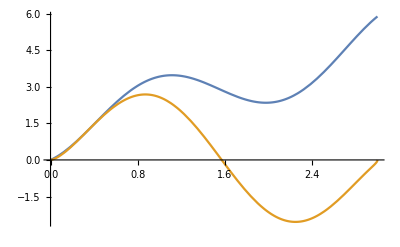

```mathematica
-4 k1 (2 k1 √(r1/k1-1) Cosh[2 d k1 √(r1/k1-1)] Sin[k1 (1-2 L1+L2)]+((2 k1-r1) Cos[k1 (1-2 L1+L2)]+r1 Cos[k1 (-1+2 L1+L2)]) Sinh[2 d k1 √(r1/k1-1)])
```

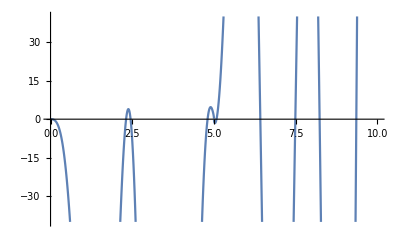

```mathematica
Plot[DetDef[k1,0,1,0.5,5],{k1,0,10},PlotRange->{{0,10},{-40,40}},PlotPoints->600]
```

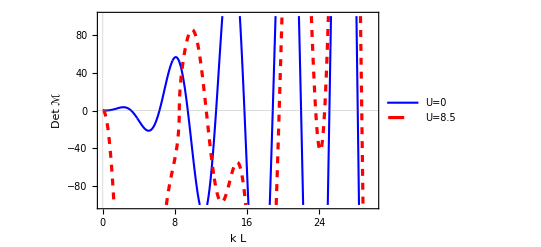

```mathematica
Plot[{DetDef[k1/3,0,1,0.5,0],DetDef[k1/3,0,1,0.5,8]},{k1,0,30},PlotRange->{{0,30},{-100,100}},PlotPoints->60000,PlotTheme->"Scientific",PlotRange->{{0.1,100000},{-0.01,1.1}},PlotStyle->{{Blue,AbsoluteThickness[1.5]},{Dashed,Red,AbsoluteThickness[2.3]},{DotDashed,Black,AbsoluteThickness[2.]}},FrameLabel->{{HoldForm[Det ℳ ],None},{HoldForm[k L],None}},PlotLabel->None,LabelStyle->{FontFamily->"Latin Modern Roman",16,GrayLevel[0]},PlotLegends->Placed[{"U=0","U=8.5","Classical"},{0.06,0.76}]]
```

```mathematica
Export["DetParr1.png",Plot[{DetDef[k1/3,0,1,0.5,0],DetDef[k1/3,0,1,0.5,8]},{k1,0,30},PlotRange->{{0,30},{-40,40}},PlotPoints->60000,PlotTheme->"Scientific",PlotRange->{{0.1,100000},{-0.01,1.1}},PlotStyle->{{Blue,AbsoluteThickness[1.5]},{Dashed,Red,AbsoluteThickness[2.3]},{DotDashed,Black,AbsoluteThickness[2.]}},FrameLabel->{{HoldForm[Det ℳ ],None},{HoldForm[k L],None}},PlotLabel->None,LabelStyle->{FontFamily->"Latin Modern Roman",16,GrayLevel[0]},PlotLegends->Placed[{"U=0","U=8","Classical"},{0.06,0.76}]],ImageResolution->1*160]
```

DetParr1.png

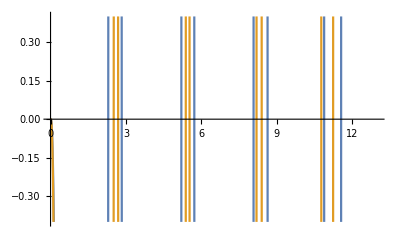

```mathematica
Plot[{DetDef[k1,0,1,0.125,10],DetDef[k1,0,1,0.25,10]},{k1,0,12},PlotRange->{{0,13},{-0.4,0.4}},PlotPoints->600]
```

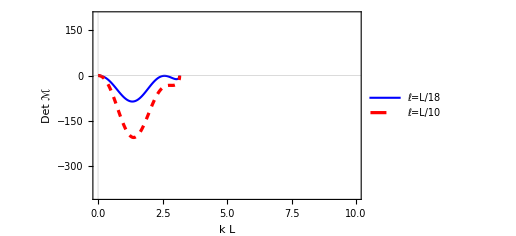

```mathematica
Plot[{DetDef[k1,0,1,0.125,10],DetDef[k1,0,1,0.25,10]},{k1,0,10},PlotRange->{{0,10},{-400,200}},PlotPoints->600,PlotTheme->"Scientific",PlotRange->{{0.1,100000},{-0.01,1.1}},PlotStyle->{{Blue,AbsoluteThickness[1.5]},{Dashed,Red,AbsoluteThickness[2.3]},{DotDashed,Black,AbsoluteThickness[2.]}},FrameLabel->{{HoldForm[Det ℳ ],None},{HoldForm[k L],None}},PlotLabel->None,LabelStyle->{FontFamily->"Latin Modern Roman",16,GrayLevel[0]},PlotLegends->Placed[{"ℓ=L/18","ℓ=L/10","Classical"},{0.06,0.82}]]
```

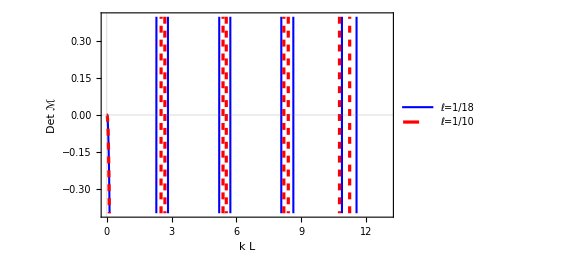

```mathematica
Export["DetParr2.png",Plot[{DetDef[k1,0,1,0.125,10],DetDef[k1,0,1,0.25,10]},{k1,0,10},PlotRange->{{0,10},{-400,200}},PlotPoints->600,PlotTheme->"Scientific",PlotRange->{{0.1,100000},{-0.01,1.1}},PlotStyle->{{Blue,AbsoluteThickness[1.5]},{Dashed,Red,AbsoluteThickness[2.3]},{DotDashed,Black,AbsoluteThickness[2.]}},FrameLabel->{{HoldForm[Det ℳ ],None},{HoldForm[k L],None}},PlotLabel->None,LabelStyle->{FontFamily->"Latin Modern Roman",16,GrayLevel[0]},PlotLegends->Placed[{"ℓ=L/18","ℓ=L/10","Classical"},{0.06,0.82}]],ImageResolution->1*160]
```

DetParr2.png

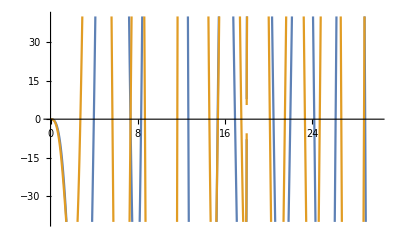

```mathematica
Plot[{DetDef[k1/3,0,2,0.5,6],DetDef[k1/3,0,3,0.5,6]},{k1,0,30},PlotRange->{{0,30},{-40,40}},PlotPoints->600]
```

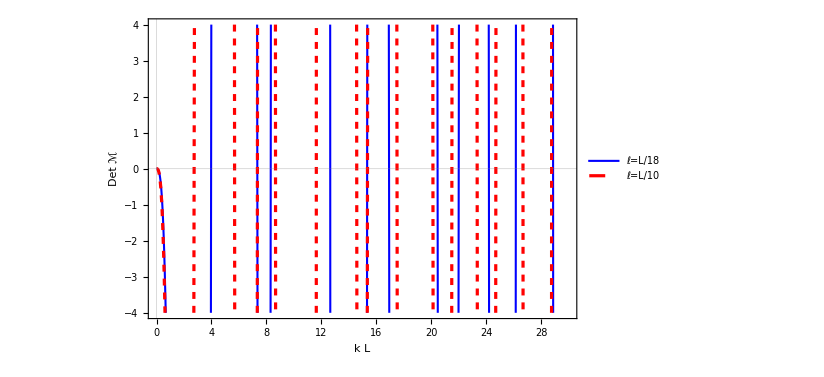

```mathematica
Plot[{DetDef[k1/3,0,2,0.5,6],DetDef[k1/3,0,3,0.5,6]},{k1,0,30},PlotRange->{{0,30},{-4,4}},PlotPoints->600,PlotTheme->"Scientific",PlotRange->{{0.1,100000},{-0.01,1.1}},PlotStyle->{{Blue,AbsoluteThickness[1.5]},{Dashed,Red,AbsoluteThickness[2.3]},{DotDashed,Black,AbsoluteThickness[2.]}},FrameLabel->{{HoldForm[Det ℳ ],None},{HoldForm[k L],None}},PlotLabel->None,LabelStyle->{FontFamily->"Latin Modern Roman",16,GrayLevel[0]},PlotLegends->Placed[{"ℓ=L/18","ℓ=L/10","Classical"},{0.06,0.76}]]
```